# TensorNetworks: Examples

This notebook demonstrates all functions in Wolfram`TensorNetworks` with detailed examples including formulas, explanations, and quantum applications.

## Setup

Install TN paclet:

```mathematica
PacletInstall["https://www.wolframcloud.com/obj/wolframquantumframework/TensorNetworks.paclet",ForceVersionInstall->True]
(*PacletDirectoryLoad["/Users/mohammadb/Documents/GitHub/TensorNetworks"]*)
Needs["Wolfram`TensorNetworks`"]
```

PacletObject[…]

## Core Tensor Network Construction

TensorNetwork creates a tensor network from tensors and their index structure. At a minimal level, one needs a list of tensor and some notation for indices that specify where contraction is being done. One can imagine a tensor network as Inactive[TensorContract][Inactive[TensorProduct][tensors],slots of contractions]

```mathematica
t1=RandomComplex[{-1-I,1+I},{3,2,3}];
t2=RandomComplex[{-1-I,1+I},{2,3}];
t3=RandomComplex[{-1-I,1+I},{4,3,2,3}];
tn=TensorNetwork[{t1,t2,t3},{{1,2,3},{2,1},{4,3,2,5}}]
```

TensorNetwork[…]

Check it is a tensor network:

```mathematica
TensorNetworkQ[tn]
```

True

Expression of contraction for TN based on TensorContract, TensorProduct and global contraction slots

```mathematica
TensorNetworkContraction[TensorNetworkData@SparseTensorNetwork@tn]
```

TensorContract[SparseArray[…]⊗SparseArray[…]⊗SparseArray[…],{{1,5},{2,4,8},{3,7}}]

Making tensors as sparse array (maybe memory save)

```mathematica
TensorNetworkContraction[SparseTensorNetwork@tn]
```

TensorContract[SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗2,2,21,2,3,{{1,5},{2,10},{3,7},{4,11},{8,12}}]

SparseTensorNetwork converts tensors in a TN to SparseArray form for memory efficiency. but not sure if it is a good name because only replacing head might not help esp since tensors are generated by RandomComplex or RandomReal

Execute the contraction

```mathematica
finalTensor=TensorNetworkContract[tn]
```

{{-1.82272+1.2499 ⅈ,0.666118+1.54877 ⅈ,-0.939243+0.800212 ⅈ},{0.393443+0.194306 ⅈ,-0.808241+0.532054 ⅈ,0.243261-2.82255 ⅈ},{-0.408784-0.771778 ⅈ,-0.692917+0.097463 ⅈ,-2.17655-1.61607 ⅈ},{-1.04592+1.87802 ⅈ,3.10521-0.483815 ⅈ,0.771263+2.16098 ⅈ}}

```mathematica
data=TensorNetworkData[SparseTensorNetwork@tn]
```

<|Tensors→{SparseArray[…],SparseArray[…],SparseArray[…]},Dimensions→{{3,2,3},{2,3},{4,3,2,3}},Hyperedges→{{1,2,3},{2,1},{4,3,2,5}},Indices→{{11,12,13},{22,21},{34,33,32,35}},Vertices→{1,2,3},Bonds→{{11,21}→3,{12,22,32}→2,{13,33}→3},Contractions→{{{11,21},{12,22,32},{13,33}},{{12,22,32},{11,21}},{34,{13,33},{12,22,32},35}},ContractionIndices→{{1,2,3},{2,1},{4,3,2,5}},FreeIndices→{4,5}|>

list of tensors

```mathematica
TensorNetworkTensors[tn]==data["Tensors"]
```

True

local indices of tensors (the contraction info is encoded in the superscripts)

```mathematica
data["Indices"]
```

{{11,12,13},{22,21},{34,33,32,35}}

Global indices of tensors, this time with explicit info of contractions (repeated are contracted)

```mathematica
TensorNetworkIndices[tn]
%==data["ContractionIndices"]
```

{{1,2,3},{2,1},{4,3,2,5}}

True

Global indices and their dimensions:

```mathematica
TensorNetworkIndexDimensions[tn]
```

{1→3,2→2,3→3,2→2,1→3,4→4,3→3,2→2,5→3}

indices of each tensor, if paired/listed with another one it means it will be contracted. If no list, it means it will be a free index

```mathematica
TensorNetworkContractions[tn]
%==data["Contractions"]
```

{{{11,21},{12,22,32},{13,33}},{{12,22,32},{11,21}},{34,{13,33},{12,22,32},35}}

True

Indices that are not being contracted

```mathematica
TensorNetworkFreeIndices@tn
```

{4,5}

Hypergraph of TN:

```mathematica
tn["Hypergraph"]
```

-Graphics-

Hyperedges:

```mathematica
tn["Hyperedges"]
```

{{1,2,3},{2,1},{4,3,2,5}}

As one can see above, the second index is shared by three tensors, meaning it is not a pairwise/binary tensor

```mathematica
BinaryTensorNetworkQ[tn]
```

False

To transform a TN that is not pairwise/binary, one can add symbolic delta-product tensor at the right places

```mathematica
BinaryTensorNetwork[SparseTensorNetwork@tn]["Tensors"]
```

{SparseArray[…],SparseArray[…],SparseArray[…],2,2,21,2,3}

```mathematica
Row[{tn["Hypergraph"],"⟶^(Make TN a binary/pairwise TN)",BinaryTensorNetwork[tn]["Hypergraph"]}]
```

-Graphics-⟶^(Make TN a binary/pairwise TN)-Graphics-

Since graph is always binary, if one asks for Graph of a TN, one gets automatically a spider (symbolic delta-product tensor) added

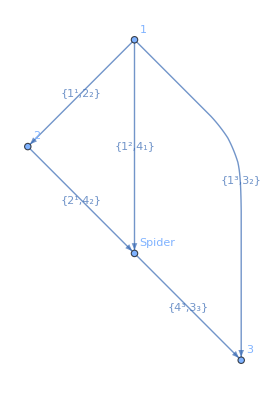

```mathematica
Graph[tn["Graph"],EdgeLabels->Automatic]
```

## Graph and Topology

### ToTensorNetworkGraph

Constructs a TensorNetwork from a graph with tensor data at vertices.

```mathematica
tng=ToTensorNetworkGraph[g=RandomGraph[{4,3}],Method->"RandomComplex"]
```

-Graphics-

```mathematica
TensorNetworkGraphQ[tng]
```

True

```mathematica
TensorNetworkGraphData[tng]
```

<|Tensors→{-0.290052-0.809619 ⅈ,{{-0.190953+0.334751 ⅈ,0.309696-0.41801 ⅈ},{0.59484-0.547468 ⅈ,0.0352163-0.0465521 ⅈ}},{{0.903186+0.40094 ⅈ,-0.540956-0.671284 ⅈ},{-0.42869-0.628794 ⅈ,0.560747-0.382486 ⅈ}},{{-0.141162-0.00628969 ⅈ,-0.537181-0.180002 ⅈ},{0.260073-0.560948 ⅈ,0.346318+0.915883 ⅈ}}},Dimensions→{{},{2,2},{2,2},{2,2}},Indices→{{},{1^1,1^2},{2^1,2_1},{4_1,4_2}},Vertices→{3,1,2,4},FreeIndices→{},Bonds→{{1^1,2_1}→2,{1^2,4_2}→2,{2^1,4_1}→2},Contractions→{{},{{1^1,2_1},{1^2,4_2}},{{2^1,4_1},{1^1,2_1}},{{2^1,4_1},{1^2,4_2}}},ContractionIndices→{{},{1^1,1^2},{2^1,1^1},{2^1,1^2}}|>

```mathematica
ToTensorNetworkGraph[g,Method->"Zero"]//TensorNetworkTensors
```

{0,{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}}

Default method

```mathematica
ToTensorNetworkGraph[g,Method->"Symbolic"]//TensorNetworkTensors
```

{3,1222,2222,4222}

```mathematica
ToTensorNetworkGraph[g,Method->"Random"]//TensorNetworkTensors
```

{0.215163,{{-0.729598,-0.5881},{-0.766384,0.321175}},{{0.646492,-0.346191},{0.474919,0.242131}},{{-0.180045,-0.536105},{0.718014,0.946202}}}

```mathematica
ToTensorNetworkGraph[g,Method->"RandomComplex"]//TensorNetworkTensors
```

{-0.081218-0.326996 ⅈ,{{-0.344506+0.202762 ⅈ,0.52723-0.220739 ⅈ},{0.907221-0.812833 ⅈ,-0.415419+0.558204 ⅈ}},{{0.0757565+0.965179 ⅈ,0.100934+0.427256 ⅈ},{0.932724+0.441156 ⅈ,0.70687-0.0317765 ⅈ}},{{0.279439+0.635598 ⅈ,0.600491+0.650481 ⅈ},{0.131945-0.367797 ⅈ,0.513666+0.82124 ⅈ}}}

Returns a graph showing index connectivity (edges represent shared indices).

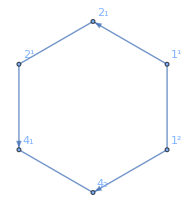

```mathematica
TensorNetworkIndexGraph[tng]
```

### RandomTensorNetwork

RandomTensorNetwork[{n vertex,m edges}, max dimension, max rank]
Given a random graph generated as RandomGraph[{n,m}] for specifying connectivity, then one can specify a max dimension and max rank. Note that vertex degree overwrites the max rank if the max rank is less than vertex degree

maybe instead of max rank, we accept additional rank (as additional tensor legs, so rank would be random[1,vertex degree+additional rank)

```mathematica
tn=RandomTensorNetwork[{4,4},3,2]
```

TensorNetwork[…]

```mathematica
TensorRank/@tn["Tensors"]
```

{3,2,2,2}

```mathematica
TensorDimensions/@tn["Tensors"]
```

{{3,2,3},{2,2},{3,2},{3,2}}

```mathematica
RandomTensorNetwork[{4,4},3,2]["Tensors"]
```

{{{-0.400922-0.675774 ⅈ,-0.341742+0.78452 ⅈ,-0.360016+0.0425217 ⅈ},{0.67753-0.339479 ⅈ,-0.132242+0.463663 ⅈ,-0.449757-0.240483 ⅈ},{-0.17203+0.786093 ⅈ,-0.587471+0.783451 ⅈ,0.653973+0.407294 ⅈ}},{{-0.664671+0.264216 ⅈ,-0.938034+0.559488 ⅈ},{0.580729+0.0064248 ⅈ,-0.77827-0.517972 ⅈ},{0.0448602+0.885219 ⅈ,0.78015+0.916662 ⅈ}},{{-0.423667-0.0760246 ⅈ,-0.993017+0.0921686 ⅈ,-0.394675-0.235423 ⅈ},{0.420644+0.803818 ⅈ,0.13553+0.0284919 ⅈ,0.531536+0.434133 ⅈ}},{{0.409565-0.0255959 ⅈ,0.454707+0.384287 ⅈ},{-0.753628+0.539522 ⅈ,0.256818+0.462552 ⅈ}}}

```mathematica
RandomTensorNetwork[{4,4},3,2,Method->"Complex"]["Tensors"]
```

{{{-0.830649-0.373232 ⅈ,-0.803914-0.938564 ⅈ,0.482234-0.239762 ⅈ},{-0.213589+0.691653 ⅈ,-0.472717-0.32462 ⅈ,-0.995612+0.597571 ⅈ}},{{-0.370817+0.50458 ⅈ,-0.168658+0.823053 ⅈ},{-0.640186+0.390626 ⅈ,0.617935-0.584025 ⅈ}},{{{-0.533745+0.283719 ⅈ,-0.677817+0.691155 ⅈ},{-0.30667+0.256263 ⅈ,-0.833121+0.634735 ⅈ},{-0.60702-0.939489 ⅈ,-0.653127+0.152081 ⅈ}},{{0.93798-0.869272 ⅈ,-0.704221-0.44272 ⅈ},{-0.617951-0.350581 ⅈ,0.825707+0.683825 ⅈ},{0.358732-0.837804 ⅈ,-0.0203683+0.109623 ⅈ}}},{{-0.819392-0.691236 ⅈ,-0.410375-0.0133173 ⅈ},{-0.264034+0.480193 ⅈ,0.51197-0.15035 ⅈ}}}

Automatic method for random real

```mathematica
RandomTensorNetwork[{4,4},3,2,Method->Automatic]["Tensors"]
```

{{{0.257315,-0.236121},{0.991936,0.0631029}},{{-0.182843,-0.673602},{-0.831425,0.38453},{0.881419,0.435887}},{{-0.849513,0.0482818,-0.239309},{0.889826,-0.423059,0.117526}},{{-0.476825,-0.67631},{0.376111,-0.63525}}}

### TensorNetworkAdd and TensorNetworkDelete

Adds a new tensor to an existing network with specified indices.

```mathematica
tn2=TensorNetwork[RandomComplex[{-1-I,1+I},{4,2,2,2}],{{1,2,3},{2,4,3},{4,5,6},{1,5,7}}]
```

TensorNetwork[…]

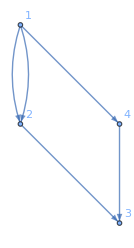

```mathematica
tn2["Graph"]
```

```mathematica
tn3=TensorNetworkAdd[tn2,PauliMatrix[1],{6,7}]
```

TensorNetwork[…]

```mathematica
tn3["Graph"]
```

-Graphics-

```mathematica
TensorNetworkDelete[tn3,-1]==tn2
```

True

### TensorNetworkReplaceIndices

### InitializeTensorNetwork

### TensorNetworkToNetGraph

### TensorNetworkRemoveCycles

## Contraction and Path Optimization

```mathematica
(*tn=(*TensorNetwork[tensors,indices]*)RandomTensorNetwork[{12,10},3]*)
```

```mathematica
dims={{3,3,2},{3,2,3},{3,3,3,3,3},{2,3},{3,3,3,3,2},{3,3},{3,3,2},{3,3,3},{2,2,2},{3,2,3,3},{3,3,3,3}};
```

```mathematica
tensors=RandomComplex[{-1-I,1+I},#]&/@dims;
```

```mathematica
indices={{1,2,3},{1,4,5},{6,7,8,9,10},{4,11},{12,2,11,13,14},{15,16},{17,15,18},{19,12,13},{20,21,22},{23,24,25,26},{6,12,27,16}};
```

```mathematica
tn=TensorNetwork[tensors,indices]
```

TensorNetwork[…]

Expression of TN contraction using TensorProduct and global contraction slots

```mathematica
TensorNetworkContraction[SparseTensorNetwork@tn]
```

TensorContract[SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗SparseArray[…]⊗3,3,31,2,3,{{1,4},{2,15},{5,12},{7,34},{13,16},{14,38},{17,26},{19,22},{20,37},{25,39},{35,40}}]

```mathematica
finalT=TensorNetworkContract[tn];//Timing
```

{13.1941,Null}

### TensorNetworkFindContractionPath

Finds an optimized contraction path using the Cotengra library.
- Optimal: The optimizer method that tries to find the best possible contraction order for the chosen objective (often slower/more exhaustive than heuristics).
- flops: Minimize total arithmetic work over the whole contraction (sum of operation counts across all contraction steps). Good if compute is the bottleneck.
- size: Minimize the peak size of any single intermediate tensor created during the contraction (a proxy for peak memory needed). Good if you’re memory-limited.
- max: Minimize the cost of the single most expensive contraction step (the “worst” step). Good if you want to avoid one step dominating runtime or failing due to a huge intermediate.
- write: Minimize total memory written/moved for intermediates (roughly the sum of sizes of all intermediate tensors produced). Good if memory bandwidth or storing intermediates (e.g., for backprop) is costly.
- combo: Minimize a weighted combination of compute and memory traffic, typically: total_flops + α  total_write. This trades off computation vs bandwidth with a tunable weight α.
- limit: Minimize a “per-step bottleneck” score that penalizes steps that are either too compute-heavy or too memory-traffic-heavy, typically aggregating something like max(step_flops, α * step_write) over steps. This aims to avoid any contraction step being an extreme outlier in either compute or memory cost.

```mathematica
paths=AssociationMap[TensorNetworkFindContractionPath[tn,Method->#]&,{"Optimal","flops","max","size","write","combo","limit"}]
```

<|Optimal→{{8,12},{2,4},{1,10},{2,9},{7,8},{6,7},{2,6},{1,5},{1,4},{1,2},{1,2}},flops→{{6,7},{9,11},{6,9},{1,2},{2,3},{6,7},{5,6},{4,5},{1,4},{1,2},{1,2}},max→{{4,5},{10,11},{6,10},{2,9},{1,8},{6,7},{2,6},{1,5},{1,4},{1,2},{1,2}},size→{{8,12},{2,4},{1,10},{2,9},{7,8},{6,7},{2,6},{1,5},{1,4},{1,2},{1,2}},write→{{6,7},{9,11},{6,9},{2,4},{1,8},{2,7},{5,6},{4,5},{1,4},{1,2},{1,2}},combo→{{6,7},{9,11},{6,9},{2,4},{1,8},{2,7},{5,6},{4,5},{1,4},{1,2},{1,2}},limit→{{6,7},{9,11},{6,9},{2,4},{1,8},{2,7},{5,6},{4,5},{1,4},{1,2},{1,2}}|>

```mathematica
methods=$TensorNetworkContractionMethods
```

{ArrayDotTranspose,ArrayDot,Dot,TensorContract,TableSum}

```mathematica
tf=Outer[Timing[ActivateTensors[TensorNetworkContraction[tn,#1,Method->#2]]]&,Values[paths],Most[methods],1];
```

```mathematica
tf//Dimensions
```

{7,4,2}

```mathematica
TableForm[tf[[All,All,1]],TableHeadings->{{"Optimal","flops","max","size","write","combo","limit"},Most[methods]}]
```

| ArrayDotTranspose | ArrayDot | Dot | TensorContract
Optimal | 4.19666 | 4.27905 | 4.30405 | 7.25306
flops | 4.26718 | 4.33723 | 4.34314 | 7.16205
max | 4.32645 | 4.25674 | 4.36773 | 7.66079
size | 4.26905 | 4.22343 | 4.28489 | 7.63129
write | 4.32726 | 4.22506 | 4.33969 | 7.44806
combo | 4.44745 | 4.26603 | 4.38971 | 7.39373
limit | 4.28924 | 4.23169 | 4.28936 | 7.47254